```mathematica
Subscript[G, MOTOR]= β α /(s+α);
Subscript[G, MOTORCONTROLLER]=Subscript[J, p]+Subscript[J, i]/s;
Subscript[G, CONTROLLEDMOTOR] = Factor[1/(1/Subscript[G, MOTOR]+Subscript[J, p]+Subscript[J, i]/s )];
Subscript[G, ANGLECONTROLLER]=Subscript[K, p]+Subscript[K, i]/s;
Subscript[G, VELOCITYTOANGLE]=-s/(L s^2- g);
Subscript[G, POSITION]=(r/s);


eq1=θ[s]==Subscript[E, v][s]*Subscript[G, VELOCITYTOANGLE]*Subscript[G, MOTOR]*Subscript[G, MOTORCONTROLLER];
eq2=V[s]==Subscript[E, v][s]*Subscript[G, MOTOR]*Subscript[G, MOTORCONTROLLER];
eq3=Subscript[E, v][s]==Subscript[E, θ][s]*Subscript[G, ANGLECONTROLLER];
eq4=Subscript[E, θ][s]==Subscript[θ, d][s]-θ[s]+V[s]*Subscript[G, POSITION];

sol=Solve[{eq1,eq2,eq3,eq4},{θ[s],V[s],Subscript[E, v][s],Subscript[E, θ][s]}][[1]];
Subscript[G, TOTALSYSTEM]=Factor[(θ[s]/Subscript[θ, d][s])/.sol];
```

## Testing Transfer Function

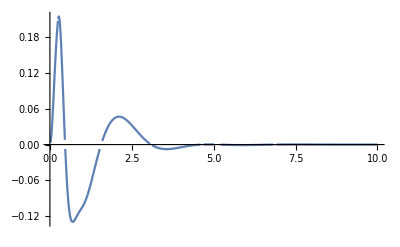

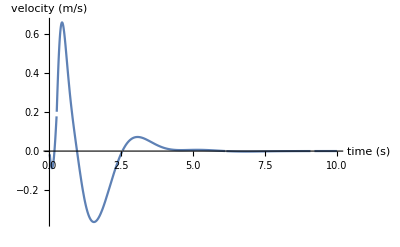

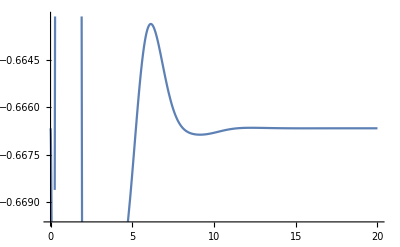

```mathematica
Subscript[θ, d][t]=(UnitStep[t]-UnitStep[t-1/4])/15;
parameters = {g-> 98/10, L-> 1/10, α-> 14, β-> 1/400, Subscript[J, p]-> 10, Subscript[J, i]->65,Subscript[K, p]->-78.6,Subscript[K, i]->-62.24,r->-0.1};
parameters2 = {g-> 98/10, L-> 1/10, α-> 14, β-> 1/400};
parameters3 = {g-> 98/10, L-> 1/10, α-> 14, β-> 1/400,Subscript[J, p]->10,Subscript[J, i]->69};
poles := Values[NSolve[Denominator[Subscript[G, TOTALSYSTEM]]==0,s]/.parameters3];
Subscript[G, fullsystemsubbed]=Subscript[G, TOTALSYSTEM]/.parameters;

thetaResponse=InverseLaplaceTransform[Subscript[G, fullsystemsubbed]*LaplaceTransform[Subscript[θ, d][t],t,s],s,t];
vResponse =InverseLaplaceTransform[Subscript[G, fullsystemsubbed] LaplaceTransform[Subscript[θ, d][t],t,s]/(Subscript[G, VELOCITYTOANGLE]/.parameters),s,t];
xResponse =Integrate[vResponse,t];
Plot[thetaResponse,{t,0,10},PlotRange->All]
Plot[vResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "velocity (m/s)"}]
Plot[xResponse,{t,0,20}]
```

## Visualize Poles

```mathematica
Manipulate[ListPlot[ReIm[poles/.{Subscript[K, p]-> Kp, Subscript[K, i]-> Ki,r->w}],PlotRange-> {{-30,30},{-30,30}},PlotMarkers-> {Graphics[{Blue,Disk[]}],.025},AxesLabel->{"Re","Im"}],{Kp,0,-10000},{Ki,0,-10000},{w,0,-10}]
```

## Calculate Poles

```mathematica
poles/.{r->-0.1,Subscript[K, p]->-78.6,Subscript[K, i]->-62.2}
```

{{-4.47672-9.76347 ⅈ},{-4.47672+9.76347 ⅈ},{-1.73142-1.81269 ⅈ},{-1.73142+1.81269 ⅈ},{-0.791862-1.18475 ⅈ},{-0.791862+1.18475 ⅈ}}

## Minimizing Poles

```mathematica
f[kpvval_, kivval_]:=N[Max[Re[Values[Solve[Denominator[Factor[Subscript[G, TOTALSYSTEM]/.parameters2/.{Subscript[K, p]->kpvval,Subscript[K, i]-> kivval,Subscript[J, p]-> 10,Subscript[J, i]->65,r-> -.1}]]==0,s]]]]]
```

```mathematica
NMinimize[f[Subscript[k, p],Subscript[k, i]],{Subscript[k, p],Subscript[k, i]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-1.11644,{k_p→-84.1656,k_i→-64.3697}}